```mathematica
m = 94;
f = 300;
c = 1.7
```

1.7

```mathematica
sol = NDSolve[{x''[t] == f/m - c/m*x'[t]^2, x[0] == 0, x'[0] == 0}, x, {t, 0, 10}]
```

{{x→InterpolatingFunction[…]}}

```mathematica
Plot[x[t]/.sol, {t, 0, 10}]
```

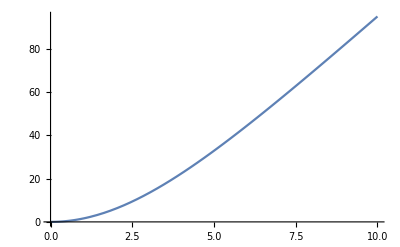

-Graphics-